```mathematica
Directory[]
```

/Users/alexis

```mathematica
SetDirectory["/Users/alexis/workspace/clustersearch/cpp/build"]
```

/Users/alexis/workspace/clustersearch/cpp/build

This function wraps the program “clusters”

```mathematica
Clusters[alpha_,length_,colors_,gray_,samples_,mode_:"stats"]:=
(* Returns means of cluster_size, perimeter_size, colors, exits_size, robustness *)
Block[{args,command,results,seed=1},
args="";
args = StringJoin[args," ", "--alpha=",     ToString[alpha]];
args = StringJoin[args," ", "--length=",   ToString[length]];
args = StringJoin[args," ", "--colors=",   ToString[colors]];
args = StringJoin[args," ", "--gray=",       ToString[gray]];
args = StringJoin[args," ", "--samples=", ToString[samples]];
args = StringJoin[args," ", "--seed=",       ToString[seed]];
args = StringJoin[args," ", "--mode=",       ToString[mode]];
args = StringJoin[args," ", "--verbose=0"];
command=StringJoin["!./clusters",args];
results =ReadList[command,Number,RecordLists->True];
If[mode=="stats",Flatten[results],results]]
```

For example, we can search one cluster given binary length-10 strings with 4 colors:.

```mathematica
Clusters[2,10,4,0,2,"data"]
```

{{265,708,3,1918,0.276226},{250,702,3,1772,0.2912}}

```mathematica
Clusters[2,10,4,0,1]
```

{265,708,3,1918,0.276226}

These help with displaying tabular output from multiple calls to Clusters

```mathematica
(* Headings of Clusters output, for labelling tabular displays.

For example:
 TableForm[<output>,TableHeadings->{None,ClustersHeadingsShort},TableAlignments->"."];
   Grid[%129~Prepend~ClustersHeadingsShort,Alignment->"."]; *)
ClustersHeadingsShort=
{"s","t","E","u","r"};
ClustersHeadingsLong={"cluster_size","perimeter_size","colors_seen","exits_size","robustness"};
```

```mathematica
ClustersTableForm[table_]:=
TableForm[table,TableHeadings->{None,ClustersHeadingsShort},TableAlignments->"."]
```

An example

Suppose that I want to
hold constant
   alpha =2
   length=10 
   samples = 15
   gray=0

let 
  colors range from 2 to 5,
 
and generate a table of  outputs from Clusters

```mathematica
(* Generate table ranging over colors from 2..5 *)
With[{alpha=2,length=8,samples=100,gray=0},
Table[Clusters[alpha,length,colors,gray,samples],
{colors,2,5}]]
```

{{127.16,123.03,1,496.46,0.499828},{76.44,151.26,2,396.76,0.332389},{41.5,117.73,3,232.4,0.252854},{21.82,80.84,3.95,126.82,0.212914}}

Display it as a table with headings

```mathematica
ClustersTableForm[%]
```

s | t | E | u | r
127.16 | 123.03 | 1 | 496.46 | 0.499828
76.44 | 151.26 | 2 | 396.76 | 0.332389
41.5 | 117.73 | 3 | 232.4 | 0.252854
21.82 | 80.84 | 3.95 | 126.82 | 0.212914

Suppose I want to generate the same table as below, but left-joining a column of colors

```mathematica
(* Generate table ranging over colors from 2..5 *)
With[{alpha=2,length=8,samples=10,gray=0},
Table[{colors}~Join~Clusters[alpha,length,colors,gray,samples],
{colors,2,5}]]
```

{{2,131.6,123.3,1,502.8,0.521294},{3,82.6,160.7,2,433.2,0.342281},{4,50.3,135.1,3,280.2,0.271682},{5,24.7,88.3,4,141.8,0.222776}}

Display it as a table with headings, adding a new heading m for colors allowed.

```mathematica
ClustersTableFormRanging[table_,rangeHeader_]:=
(* Clusters output, with a ranging input var in left col *)
TableForm[table,
TableHeadings->{None,{rangeHeader}~Join~ClustersHeadingsShort},
TableAlignments->"."]
```

```mathematica
ClustersTableFormRanging[%%,"m"]
```

m | s | t | E | u | r
2 | 131.6 | 123.3 | 1 | 502.8 | 0.521294
3 | 82.6 | 160.7 | 2 | 433.2 | 0.342281
4 | 50.3 | 135.1 | 3 | 280.2 | 0.271682
5 | 24.7 | 88.3 | 4 | 141.8 | 0.222776

We use this pick out columns to prepare arguments for ListPlot

```mathematica
PickColumn1andCol[table_,col_]:=
(* Picks cols 1 and COL from table *)
Map[( #[[{1,col}]] & ),table]
```

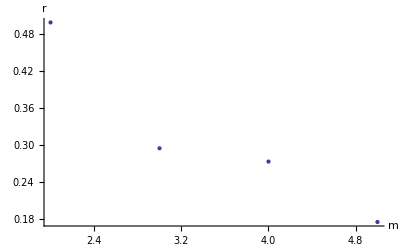

```mathematica
ListPlot[%,AxesLabel->{m,r}]
```

Now let’s do some analysis
ranging 
  colors from 2 ... 32.
with
  length=8
  alpha=2

```mathematica
(* Generate table ranging over colors from 2..5 *)
data = With[{alpha=2,length=8,samples=100,gray=0},
Table[{colors}~Join~Clusters[alpha,length,colors,gray,samples],
{colors,2,32}]]
```

{{2,126.58,125.85,1,503.58,0.496301},{3,74.45,148.44,2,386.32,0.325612},{4,38.43,112.36,2.99,215.6,0.237349},{5,15.93,62.35,3.96,93.76,0.191666},{6,9.57,43.08,4.77,57.82,0.15834},{7,5.94,29.71,5.44,37.04,0.130381},{8,5.11,26.54,6.18,32.22,0.119144},{9,3.53,20.12,6.46,22.96,0.105911},{10,2.9,17.28,6.79,19.28,0.0867411},{11,2.53,15.68,7.25,17.02,0.0863608},{12,2.37,15.07,7.38,16.18,0.0794941},{13,1.92,12.82,7.47,13.48,0.0621012},{14,2.08,13.7,8.04,14.44,0.0762817},{15,1.92,12.93,8.18,13.46,0.0699792},{16,1.96,13.11,8.11,13.72,0.0673056},{17,1.75,12.11,8.19,12.5,0.0588512},{18,1.65,11.52,7.97,11.9,0.0493125},{19,1.5,10.76,7.85,11,0.0410417},{20,1.67,11.6,8.34,12,0.0501012},{21,1.87,12.68,9.06,13.2,0.0645357},{22,1.45,10.46,8.15,10.7,0.0396042},{23,1.35,9.99,7.91,10.1,0.0340833},{24,1.54,11.06,8.59,11.24,0.0522083},{25,1.35,9.98,8.27,10.1,0.0347083},{26,1.25,9.43,8,9.5,0.02575},{27,1.41,10.32,8.51,10.44,0.0397917},{28,1.44,10.47,8.83,10.62,0.041375},{29,1.39,10.17,8.48,10.34,0.0344345},{30,1.27,9.56,8.19,9.6,0.0289583},{31,1.27,9.56,8.19,9.62,0.0279167},{32,1.34,9.91,8.5,10.02,0.0322917}}

```mathematica
(* Generate table ranging over colors from 2..5 *)
bigdata2 = 
Table[
{gray,
With[{alpha=2,length=8,samples=8000,gray=gray},
Table[{colors}~Join~Clusters[alpha,length,colors,gray,samples],
{colors,4,64,1}]]},
{gray,0.1,1,0.05}];
```

```mathematica
bigdataold=bigdata;
```

```mathematica
bigdata=bigdata2;
```

```mathematica
PlotEWithGray[grayvalue_]:=
With[
{valueindex=4,
valuelabel="E"},
Module[
{grayindex =Position[(#[[1]]&) /@ bigdata,grayvalue][[1,1]],
plottable},
plottable = PickColumn1andCol[bigdata[[grayindex]][[2]],valueindex];
Tooltip[
ListPlot[
plottable,
AxesLabel->{m,valuelabel},
PlotRange->
 Automatic 
 (* {{0,64},{6*(1-grayvalue),12*(1-grayvalue)}}  *)
],
StringJoin["g=",ToString[grayvalue]]]
]]
```

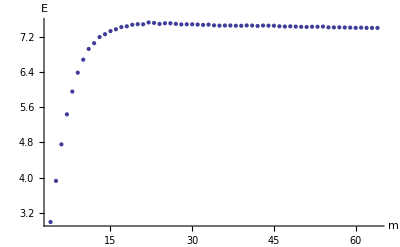

```mathematica
PlotEWithGray[0.2]
```

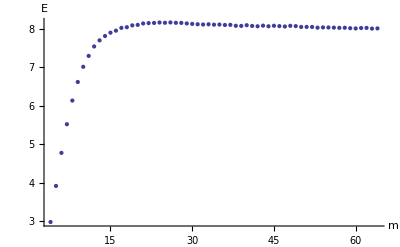
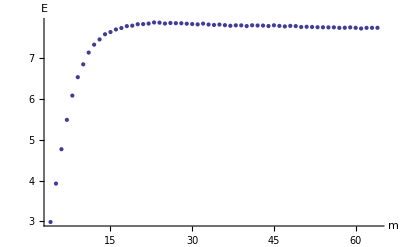
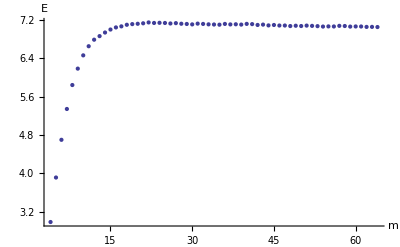
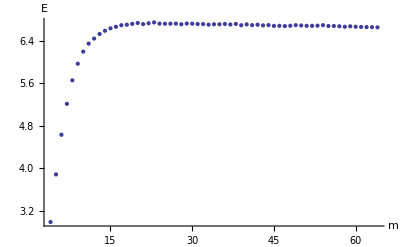
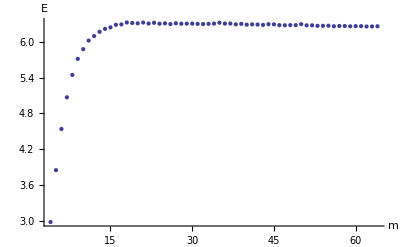
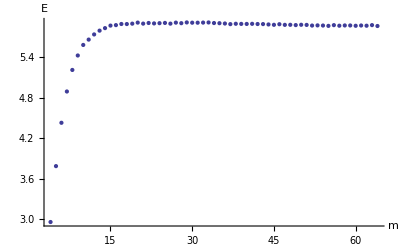
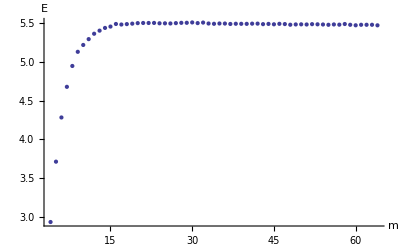
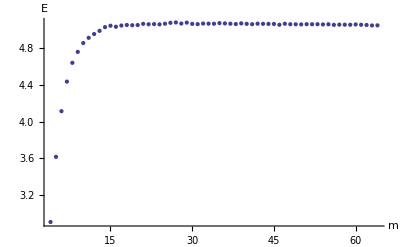
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[PlotEWithGray[g],{g,0.1,1,0.05}]
```

```mathematica
5
```

5

```mathematica
Position[(#[[1]]&) /@ bigdata,.2][[1,1]]
```

2

```mathematica
#[[1]] &/@ bigdata
```

{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}

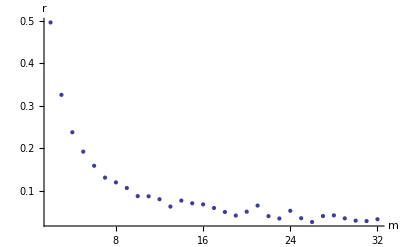

```mathematica
ListPlot[PickColumn1andCol[%247,6],AxesLabel->{m,r}]
```

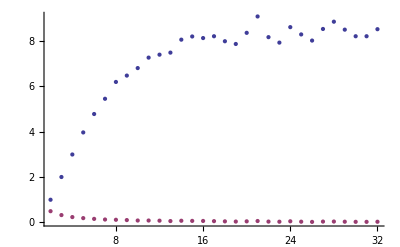

```mathematica
ListPlot[
With[
{data=data
(*
With[{alpha=2,length=8,samples=100,gray=0},
Table[{colors}~Join~Clusters[alpha,length,colors,gray,samples],
{colors,2,32}]]
*)
},
List[
PickColumn1andCol[data,4],
PickColumn1andCol[data,6]]],
AxesLabel->{m}
]
```

```mathematica
Range[2,32] // Length
```

31

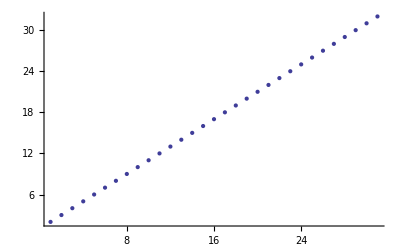

```mathematica
ListPlot[Range[2,32]]
```

```mathematica
bigdata
```

{{0.1,{{4,63.7334,145.957,2.97912,342.375,0.300271},{5,28.5792,94.8521,3.91662,164.058,0.225408},{6,12.6977,53.0204,4.7755,75.7232,0.179217},{7,7.08925,34.3399,5.51975,43.638,0.150693},{8,4.76987,25.4477,6.1345,30.1977,0.129186},{9,3.604,20.6099,6.6175,23.411,0.112862},«50»,{60,1.13725,8.80113,8.00875,8.823,0.0152948},{61,1.13425,8.785,8.01925,8.8055,0.0150901},{62,1.13088,8.76575,8.0225,8.78525,0.0147464},{63,1.1285,8.75275,8.00463,8.771,0.0145432},{64,1.12637,8.7405,8.00962,8.758,0.0143099}}},«17»,{1.,{«1»}}}

```mathematica
rawdata = Clusters[2,30,40,0,5000,"data"];
```

```mathematica
Table[rawdata[[i]],{i,1,5}] // ClustersTableForm
```

s | t | E | u | r
1 | 30 | 21 | 30 | 0
1 | 30 | 22 | 30 | 0
1 | 30 | 19 | 30 | 0
7 | 192 | 39 | 196 | 0.0666667
1 | 30 | 21 | 30 | 0

```mathematica
Max[ #⟦5⟧ & /@ rawdata] // (Exp[100 * #] &)
```

1530.47

```mathematica
SelectEandr[clustersdata_]:=Map[({#⟦3⟧,#⟦5⟧ }&),clustersdata]
```

```mathematica
PlotEandr[clustersdata_]:=ListPlot[SelectedEandr[clustersdata],AxesLabel->{"E","r"}]
```

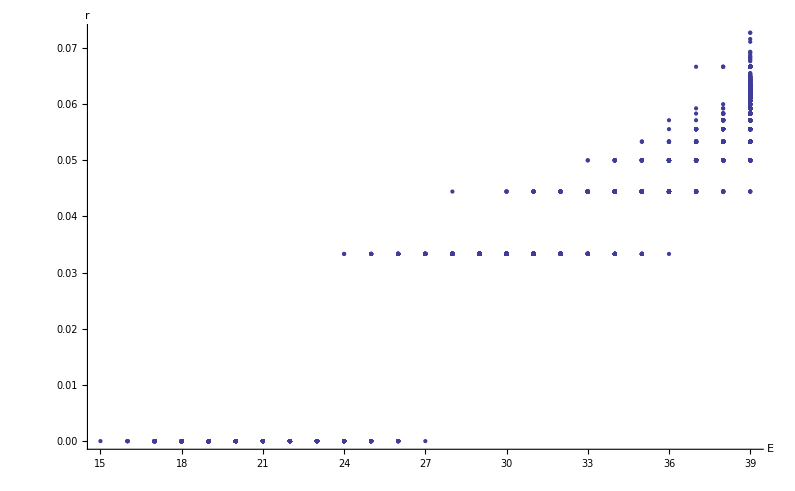

```mathematica
ListPlot[SelectEandr[rawdata],AxesLabel->{"E","r"}]
```

```mathematica
rawdata[30] = Clusters[2,30,30,0,5000,"data"];
rawdata[32] = Clusters[2,30,32,0,5000,"data"];
rawdata[35] = Clusters[2,30,35,0,5000,"data"];
rawdata[40] = Clusters[2,30,40,0,5000,"data"];
rawdata[60] = Clusters[2,30,60,0,5000,"data"];
rawdata[100] = Clusters[2,30,100,0,5000,"data"];
```

```mathematica
AbsoluteTiming[
rawdata12[30] = Clusters[2,12,6,0,5000,"data"];
rawdata12[32] = Clusters[2,12,12,0,5000,"data"];
rawdata12[35] = Clusters[2,12,18,0,5000,"data"];
rawdata12[40] = Clusters[2,12,24,0,5000,"data"];
rawdata12[60] = Clusters[2,12,32,0,5000,"data"];
rawdata12[100] = Clusters[2,12,64,0,5000,"data"];]
```

{141.32454,Null}

```mathematica
Histogram3D[
Map[SelectEandr,{rawdata[30],rawdata[35],rawdata[40],rawdata[60],rawdata[100]}],AxesLabel->{"E","r"}]
```

-Graphics3D-

```mathematica
?Listable
```

Listable is an attribute that can be assigned to a symbol f to indicate that the function f should automatically be threaded over lists that appear as its arguments.